# ЛР1. Актуализация знаний 1-ого семестра.

## 1. Работаем со списками и элементарными вычислениями.

### 1.1

Докажите эмпирически (с помощью вычислений) сходимость числового ряда ∑_(n=0)^∞ (-1)^n/(2n+1).  Сделайте предположение о том, к какому числу сходится ряд. Подтвердите вычисления графически.

```mathematica
(*Члены последовательности от 0 до n-го:*)
n:=50;
(-1)^#/(2#+1)&/@Range[0,n]
```

```mathematica
(*Их сумму могу посчитать с помощью Total:*)
(-1)^#/(2#+1)&/@Range[0,n]//Total//N
```

```mathematica
(*Все суммы от 0 членов:*)
Sum[(-1)^i/(2i+1),{i,0,#}]&/@Range[0,10]
(*Или из палитры:*)
∑_(i=0)^# (-1)^i/(2i+1)&/@Range[0,10]
```

```mathematica
(*Приближенные суммы числового ряда называются частичными суммами числового ряда. Сумма из n первых членов числового ряда называется n-й суммой ряда. Попробую посчитать предел*)
Limit[Sum[(-1)^i/(2i+1),{i,0,im}],im->Infinity]
```

```mathematica
pl1=ListPlot[Sum[(-1)^i/(2i+1),{i,0,#}]&/@Range[0,100]];
pl2=Plot[{Pi/4},{x,0,100}, Axes->True];
Show[pl1,pl2]
(*Из графика видно, что сходится к значению, посчитанному выше: Pi/4*)
```

### 1.2

Докажите эмпирически расходимость  ряда. ∑_(n=1)^∞ 1/n. Для этого можно доказать, что для любого числа K, существует N, такое что ∑_(n=1)^N 1/n> K.

### Пример

```mathematica
1/(#!)&/@Range[0,30](*Первый 31 член ряда*)
```

```mathematica
1/(#!)&/@Range[0,30]//Total//N[#,30]&(*Частичная сумма первых 31 члена*)
```

```mathematica
ⅇ-(1/(#!)&/@Range[0,30]//Total//N[#,30]&)(*Предполагаем, что ряд сходится к экпоненте*)
```

```mathematica
Table[Abs[ⅇ-(1/(#!)&/@Range[0,i]//Total)],{i,1,30}]//N[#,50]&(*смотрим, как погрешность изменяется с увеличением количества членов ряда*)
```

### Решение.

```mathematica
(*Посмотрю первые 50 членов ряда*)
1/#&/@Range[1,50]
```

```mathematica
(*Посмотрел. Посчитаю частичную сумму первых 50 членов ряда*)
1/#&/@Range[1,50]//Total//N
(*//N[#,20]& для точности*)
```

```mathematica
(*Пускай, наверное, ряд сходится к 4.5*)
4.5-(1/#&/@Range[1,50]//Total//N)
```

```mathematica
(*Но можно посчитать больше членов ряда, он не стремится к 4.5*)
1/#&/@Range[1,60]//Total//N
```

```mathematica
(*Cмотрю, как погрешность изменяется с увеличением количества членов ряда*)
Table[Abs[4.5-(1/#&/@Range[1,i]//Total)],{i,1,60}]
(*Сначала стремилась к нулю, а потом снова стала возрастать после суммы первых 50 членов*)
```

## 2. Пишем собственные функции.

### Вычисление числа π методом Монте-Карло. Теория.

Идея метода в случайном распределении точек. Зададим некоторое количество случайных точек в квадрате 0 ≤ x ≤ 1, 0 ≤ y ≤ 1.

```mathematica
Short[pts=RandomReal[{0,1},{1000,2}]]
```

Очевидно, что геометрически точки будут лежать внутри квадарата со строной 1. Если вписать в этот квадрат окружность, то логично, что часть точек окажется в ней.

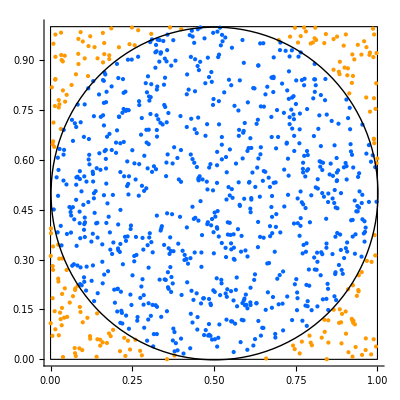

Далее логично предположить, что отношение площадей фигур будет “равно” или, лучше сказать, “близко”, отношению количества точек внутри каждой фигуры. 
Тогда если K - это количество точек в круге, а N - общее количество точек  (лежащих в квадрате), то K/N=S_круга/S_квадарата. 
Площади круга и квадарта мы можем вычислить. S_круга=π*1/4, S_квадрата=1.  
Получаем финальное соотношение, откуда выражаем π. π = 4 * K/N.

Остаётся только найти количечество точек внутри окружности исходя из геометрических свойств. С увеличением количества точек, ожидаем увеличение точности.

### 2.1

Реализуйте функцию для вычисления числа π методом Монте-Карло. На вход функция принимает, количество точек. Исследуйте, как меняется точность вычислений с увеличением количества точек.

### Решение.

```mathematica
GetPi[n_]:=(4*Length[Select[RandomReal[{0,1},{n,2}],(#[[1]]-0.5)^2+(#[[2]]-0.5)^2<=0.5^2&]])/n
```

```mathematica
(*Проверяю*)
n1=100;
n2=1000;
n3=10000;
n4=100000;
n5=1000000;
GetPi[n1]//N
GetPi[n2]//N
GetPi[n3]//N
GetPi[n4]//N
GetPi[n5]//N
```

```mathematica
Manipulate[GetPi[a],{a,1,10000}]
```

## 3. Вспоминаем графические примитивы.

Модифицируйте функцию из задания 2.1 таким образом, чтобы она также возвращала графическую визуализацию работы метода.

### Решение.

```mathematica
showPoints[n_]:=Graphics[{Thick,Line[{{0,0},{0,1},{1,1},{1,0},{0,0}}],Thick,Circle[{0.5,0.5},0.5],Hue[0.07,0.9,0.84],Point[Select[RandomReal[{0,1},{n,2}],(#[[1]]-0.5)^2+(#[[2]]-0.5)^2>=0.5^2&]],Hue[0.65,0.86,0.76],Point[Select[RandomReal[{0,1},{n,2}],(#[[1]]-0.5)^2+(#[[2]]-0.5)^2<=0.5^2&]]},PlotRange->{{0,1},{0,1}},Axes->True]
showOnlyPoints[n_]:=Graphics[{Hue[0.07,0.9,0.84],Point[Select[RandomReal[{0,1},{n,2}],(#[[1]]-0.5)^2+(#[[2]]-0.5)^2>=0.5^2&]],Hue[0.65,0.86,0.76],Point[Select[RandomReal[{0,1},{n,2}],(#[[1]]-0.5)^2+(#[[2]]-0.5)^2<=0.5^2&]]},PlotRange->{{0,1},{0,1}},Axes->True]
```

```mathematica
showPoints[n1]
showOnlyPoints[n1]
```

```mathematica
showPoints[n2]
showOnlyPoints[n2]
```

```mathematica
showPoints[n3]
showOnlyPoints[n3]
```

```mathematica
Manipulate[showPoints[a],{a,1,5000}]
```

```mathematica
Manipulate[showOnlyPoints[a],{a,1,5000}]
```

## 4. Динамические вычисления.

### 4.1.

Реализуйте функцию, принимающую на вход полином и возвращающую все его корни, а также графическую интерпретацию действительных корней.

### Пример.

Пусть задано уравнение.

```mathematica
eqn = x^7+7 x^3+x^2+11==0
```

```mathematica
eqn//Solve//Values//N//Flatten 
(*Получили корни*)
```

```mathematica
rootsreal=eqn//Solve//Values//N//Flatten//Cases[#,_Real]&
(*Вот так можно получить дествительные корни*)
```

Для получение визуализации лучше использовать функцию Plot с опцией Epilog.

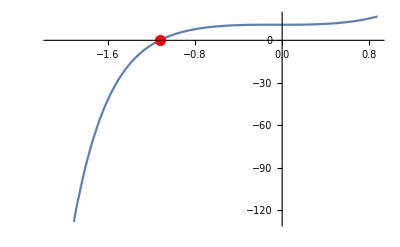

### Решение.

```mathematica
eqn1 = x^7+7 x^3+x^2+11==0
eqn2=x^8+x^4+1==0
eqn3=x^3+6 x^2-9x==0
eqn4=x^5-2 x^4+x^3-x^2-2x+1==0
```

```mathematica
(*Функция,принимающую на вход полином и возвращающая все его корни*)
getPolyRoots[poly_]:=poly//Solve//Values//N//Flatten 
(*Функция,принимающую на вход полином и возвращающая все его действительные корни*)
getPolyRootsReal[poly_]:=poly//Solve//Values//N//Flatten //Cases[#,_Real]&
```

```mathematica
(*Проверяю:*)
getPolyRoots[eqn1]
getPolyRootsReal[eqn1]
```

```mathematica
getPolyRoots[eqn2]
getPolyRootsReal[eqn2]
```

```mathematica
getPolyRoots[eqn3]
getPolyRootsReal[eqn3]
```

```mathematica
getPolyRoots[eqn4]
getPolyRootsReal[eqn4]
```

```mathematica
(*Функция для графической визуализации действительных корней полинома*)
showPolyRootsReal[poly_]:=Plot[poly,{x,-10,10},Epilog->{PointSize[Medium],RGBColor[0.5,0.03,0.5],Point[{#,0}&/@Cases[Flatten[N[Values[Solve[poly]]]],_Real]]},PlotRange->{{-10,10},{-10,10}}]
```

```mathematica
(*Проверяю*)
showPolyRootsReal[eqn1]
```

```mathematica
showPolyRootsReal[eqn2]
```

```mathematica
showPolyRootsReal[eqn3]
```

```mathematica
showPolyRootsReal[eqn4]
```

### 4.2

Реализуйте с помощью функции Manipulate скрипт аналогичный предыдущему. Теперь один из коэффициентов полинома - параметр. Продемонстируйте изменения графической интерпретации при изменении параметра.

### Решение.

```mathematica
eqn5=x^7+7 x^3+a*x^2+11==0
eqn6=a*x^3+6 x^2-9x==0
eqn7=-a*x^5-2 x^4-a*x^3-a*x^2-2x+1==0
```

```mathematica
(*Функция,принимающую на вход полином и возвращающая все его корни, их изменения в зависимости от параметра*)
getPolyParametricRoots[poly_]:=Manipulate[poly//Solve//Values//N//Flatten ,{a,-10,10}]
(*Функция,принимающую на вход полином и возвращающая все его действительные корни, их изменения в зависимости от параметра*)
getPolyParametricRootsReal[poly_]:=Manipulate[poly//Solve//Values//N//Flatten //Cases[#,_Real]&,{a,-10,10}]
```

```mathematica
(*Проверяю*)
getPolyParametricRoots[eqn5]
getPolyParametricRootsReal[eqn5]
```

```mathematica
getPolyParametricRoots[eqn6]
getPolyParametricRootsReal[eqn6]
```

```mathematica
getPolyParametricRoots[eqn7]
getPolyParametricRootsReal[eqn7]
```

```mathematica
(*Функция, показывающая изменения графической интерпритации при изменении параметра*)
showPlotChanges[poly_]:=Manipulate[Plot[poly,{x,-10,10},Epilog->{PointSize[Medium],RGBColor[0.5,0.03,0.5],Point[{#,0}&/@Cases[Flatten[N[Values[Solve[poly]]]],_Real]]},PlotRange->{{-10,10},{-10,10}}],{a,-10,10}]
```

```mathematica
showPlotChanges[eqn5]
```

```mathematica
showPlotChanges[eqn6]
```

```mathematica
showPlotChanges[eqn7]
```

### 4.3

Реализуйте функцию принимающую на вход полином и возвращающую все его корни, а также графическую интерпретацию комплексных корней. Комплексные корни стоит отрисовать на комплексной плоскости.  Подпишите их.

### Решение.

```mathematica
(*Функция,принимающую на вход полином и возвращающая все его комплексные корни*)
getPolyRootsComp[poly_]:=poly//Solve//Values//N//Flatten //Cases[#,_Complex]&
```

```mathematica
(*Проверяю*)
getPolyRootsComp[eqn1]
```

```mathematica
getPolyRootsComp[eqn2]
```

```mathematica
getPolyRootsComp[eqn4]
```

```mathematica
(*функция для графической интерпритации комплексных корней*)
showPolyRootsComp[poly_]:=Show[ComplexListPlot[getPolyRootsComp[poly],PlotStyle->Orange,PlotRange->{{-3,3},{-3,3}}],Graphics[{Text[#,{Re[#]+0.1,Im[#]+0.1}]&/@getPolyRootsComp[poly]}]]
```

```mathematica
showPolyRootsComp[eqn1]
```

```mathematica
showPolyRootsComp[eqn2]
```

```mathematica
showPolyRootsComp[eqn4]
```

### Задача

График касательной к функции с помощью Manipulate.

```mathematica
(*Уравнение касательной к графику функции y=f(x)*)
(*Сама функция*)
f1[x_]:=x^2
pl1=Plot[f1[x],{x,-5,5}]
```

```mathematica
kasat[f_,x0_]:=f[x0]+D[f[x],x]/.x->x0*(x-x0)//Expand
kasat[f1,4]
```

```mathematica
pl3=Plot[4+4 (-2+x),{x,-5,5}];
Show[pl1,pl3]
```

```mathematica
kasat[f1,5]
```

```mathematica
pl4=Plot[25+10 (-5+x),{x,-5,5}];
Show[pl1,pl4,PlotRange->{{-5,10},{0,40}}]
```

```mathematica
Manipulate[kasat[f1,a],{a,-5,5}]
```

```mathematica
Manipulate[Show[Plot[Evaluate@kasat[f1,a],{x,-5,5},PlotRange->{{-5,5},{-5,5}}],Plot[f1[x],{x,-5,5}]],{a,-5,5}]
```

```mathematica
ShowKasFun[f_]:=Manipulate[Show[Plot[Evaluate@kasat[f,a],{x,-5,5},PlotRange->{{-5,5},{-5,5}}],Plot[f1[x],{x,-5,5}]],{a,-5,5}]
```

```mathematica
ShowKasFun[f1]
```